# Sample complexity plots

This notebook computes the sample complexity for soft and hard decision fusion type networks.

### Copyright notice

Copyright (C) 2012 Donagh Horgan.
Email: donaghh@rennes.ucc.ie.

This program is free software : you can redistribute it and/or modify
it under the terms of the GNU General Public License as published by
the Free Software Foundation, either version 3 of the License, or
(at your option) any later version.

This program is distributed in the hope that it will be useful,
but WITHOUT ANY WARRANTY; without even the implied warranty of
MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE. See 
COPYING for more details.

You should have received a copy of the GNU General Public License
along with this program. If not, see http://www.gnu.org/licenses.

### Version information

09/08/2012
1.0

### Changelog

Version 1.0: This version is similar to the code used to generate the plots in the submitted version of the paper.

## Set up

Clear all symbol values and load function definitions:

```mathematica
ClearAll["Global`*"];
```

```mathematica
path=NotebookDirectory[];
SetDirectory[ToFileName[path]];
ParallelEvaluate[AppendTo[$Path,path]];
ParallelEvaluate[<<definitions.m];
<<definitions.m
<<PlotLegends`
```

## Variables

Here, we define the parameters to be used:

```mathematica
n=Range[50];
snrdb=-21;
pf=0.1;
pd=0.9;
```

```mathematica
γ=10^(snrdb/10);
```

## Calculations

### Optimised hard decision

```mathematica
OptimisedHardDecisionSampleComplexity[γ_,pf_,pd_,n_]:=Module[{λ0,f,M,result},
Off[FindRoot::lstol,FindRoot::jsing];
f[M_?NumericQ]:=Min[Table[ProbabilityOfMissedDetection[M,γ,λ0,n,k,DecisionBits->1]/.FindRoot[ProbabilityOfFalseAlarm[M,λ0,n,k,DecisionBits->1]==pf,{λ0,M}],{k,n}]];
result=M/.FindRoot[f[M]==1-pd,{M,SampleComplexity[γ,pf,pd,n]}];
On[FindRoot::lstol,FindRoot::jsing];
result
]
```

```mathematica
hard=Table[OptimisedHardDecisionSampleComplexity[γ,pf,pd,n0],{n0,n}];
```

### Approximately optimal hard decision

```mathematica
ApproximateHardDecisionSampleComplexity[γ_,pf_,pd_,n_]:=Module[{λ0,f,M,result,k=⌈n/2⌉},
Off[FindMinimum::lstol,FindRoot::lstol,FindRoot::jsing];
f[M_?NumericQ]:=Max[{ProbabilityOfMissedDetection[M,γ,λ0,n,k,DecisionBits->1],ProbabilityOfFalseAlarm[M,λ0,n,k,DecisionBits->1]}/.FindMinimum[ProbabilityOfFalseAlarm[M,λ0]+ProbabilityOfMissedDetection[M,γ,λ0],{λ0,M,1,10M}][[2]]];
result=M/.FindRoot[f[M]==1-pd,{M,1.8SampleComplexity[γ,pf,pd,n],1,10SampleComplexity[γ,pf,pd,n]}];
On[FindMinimum::lstol,FindRoot::lstol,FindRoot::jsing];
result
]
```

```mathematica
approx=Table[ApproximateHardDecisionSampleComplexity[γ,pf,pd,n0],{n0,n}];
```

### Optimised soft decision

```mathematica
soft=Table[SampleComplexity[γ,pf,pd,n0,DecisionBits->∞],{n0,n}];
```

## Results

### Plots

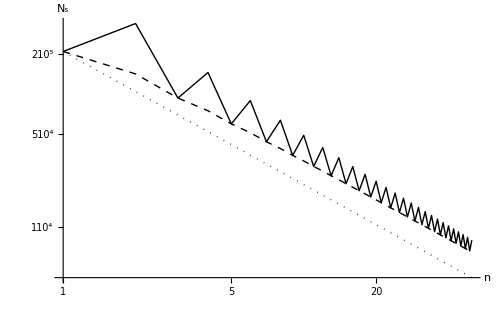

```mathematica
ListLogLogPlot[{hard,approx,soft},Joined->True,PlotRange->Full,GridLines->Automatic,AxesLabel->{"n","N_s"},PlotStyle->{{Black, Dashed},Black,{Black,Dotted}},PlotLegend->{"Hard decision","Approximation","Soft decision"},LegendPosition->{0.3,0},LegendSize->{0.6,0.5},LegendShadow->None,ImageSize->500]
```